Read me

This notebook can be used to reproduce the results shown in panel b of Fig. 5 of “Online quantum time series processing with random oscillator networks” (https://arxiv.org/abs/2108.00698) in the manner described in the preprint. It requires a working installation of a recent version of Wolfram Mathematica. It has been tested in Wolfram Mathematica 11.2 for Microsoft Windows (64-bit). 

To use it, evaluate Sections 1 and  2.1 first. The parameter “realizations” controls how many samples are used to generate the ensemble averages and is by default set to 100. In “Online quantum time series processing with random oscillator networks” a value of 100 has been used.

Then you can proceed with 2.2. Inside this subsection cells should in general be evaluated in order, i.e. plots can be made only after data has been generated and so on. Subsection 2.3 only contains results computed previously, to reproduce these computations use the notebook Figure 5a partial generalizations.

Both 2.2 and 2.3 need to be evaluated before 2.4 which simply combines the results into a single figure. 

The author of this notebook is Johannes Nokkala. Any inquiries about its contents can be sent to jsinok@utu.fi

Summary of the license
This work is licensed under CC BY 4.0. You are free to share and adapt the material as long as it remains under the same license  and you give appropriate credit. For the full legal text see LICENSE in the main repository: https://github.com/jsinok/onlinequantumtimeseries

1 Preliminaries

We will clear all values, definitions, attributes, messages, and defaults associated with symbols in the global context. This is to prevent problems with pre-existing symbol definitions.

```mathematica
ClearAll["Global`*"];
```

We will set the history length to 0 to keep memory consumption in check. That is to say none of the previous input and output lines are saved by default for later use, only the ones we explicitly keep.

```mathematica
$HistoryLength=0;
```

Parallelization is used to speed up certain parts of the computations. We launch the maximum number of them now.

```mathematica
If[$ProcessorCount-$KernelCount>0,LaunchKernels[$ProcessorCount-$KernelCount]]
```

## User-defined functions

### QHON generator

#### Auxiliary functions

```mathematica
Clear[blockArray];
blockArray[mat_]:=Developer`ToPackedArray[Normal@SparseArray[Tuples[Range@#-{1,0,0}].{Rest@#,{1,0},{0,1}}&@Dimensions@mat->Flatten@mat],Real];
```

```mathematica
Clear[completegraphrandomweights];
completegraphrandomweights[n_]:=SetProperty[CompleteGraph[n],EdgeWeight->{_:>RandomReal[{0.,2.}]}];
```

```mathematica
(*get the diagonal of a matrix*)
(*listable: list of matrices gives a list of diagonals*)
Clear[mydiagonal];
mydiagonal=Compile[{{matrix,_Real,2}},Transpose[matrix,{1,1}],RuntimeAttributes->{Listable}];
```

```mathematica
(*not currently in use*)
Clear[myouter];
myouter=Compile[{{list1stelement,_Real,1}},
Outer[Times,list1stelement,list1stelement],RuntimeAttributes->{Listable}];
```

```mathematica
(*input: weighted graph*)
(*output: corresponding weighted KirchhoffMatrix*)
Clear[weightedKirchhoffMatrix];
weightedKirchhoffMatrix[g_]:=DiagonalMatrix[Tr/@Transpose@#]-#&@WeightedAdjacencyMatrix[g]
```

```mathematica
(*input: graph, uniform coupling strength, bare frequency*)
(*output: matrix defining the Hamiltonian of a network of identical oscillators with the bare frequency, interacting with uniform coupling strengths; orthogonal matrix diagonalizing the previous matrix; frequencies in the diagonal basis*)
Clear[getmatrixA];
getmatrixA=Block[{matrixA=DiagonalMatrix[ConstantArray[#3^2 /2,VertexCount[#1]]]+#2 weightedKirchhoffMatrix[#1]/2,listK,listD},
{listD,listK}=Eigensystem[matrixA];
{matrixA,Transpose[Normalize/@listK],√(2listD)}]&;
```

```mathematica
(*input: index/indices of the system you wish to use as ancilla, total number of oscillators*)
(*output: permutation matrix P such that P.{q1,q2,..,qn,p1,p2,...,pn} gives {q1,p1,q2,p2,...,,qA1,pA1,qA2,pA2,...}*)
Clear[getPermutationmatrix];
(*single ancilla case*)
getPermutationmatrix[ancilla_,n_]:=getPermutationmatrix[ancilla,n]=IdentityMatrix[2n][[Riffle[Range[n],Range[n]+n]]].KroneckerProduct[IdentityMatrix[2],IdentityMatrix[n][[Join[Delete[Range[n],ancilla],{ancilla}]]]];

(*many ancillae*)
getPermutationmatrix[ancillas_?ListQ,n_]:=IdentityMatrix[2n][[Riffle[Range[n],Range[n]+n]]].KroneckerProduct[IdentityMatrix[2],IdentityMatrix[n][[Join[Delete[Range[n],{ancillas}ᵀ],ancillas]]]];
```

```mathematica
(*given the eigensystem of the Hamiltonian, time and ancillas, return the symplectic matrix that propagates the operators {q1,p1,q2,p2,...,,qA1,pA1,qA2,pA2,...}*)
Clear[getmatrixSΔt];
getmatrixSΔt[matrixK_,listΩ_,Δt_,ancilla_]:=
With[{matrixPermute=getPermutationmatrix[ancilla,Length[listΩ]],bigmatK=KroneckerProduct[IdentityMatrix[2],matrixK]},matrixPermute.bigmatK.ArrayFlatten[({{DiagonalMatrix[Cos[listΩ Δt]], DiagonalMatrix[Sin[listΩ Δt]/listΩ]}, {-DiagonalMatrix[Sin[listΩ Δt]listΩ], DiagonalMatrix[Cos[listΩ Δt]]}})].bigmatKᵀ.matrixPermuteᵀ];
```

#### Get ancilla state

```mathematica
(*this gives a single mode CM of a squeezed thermal state*)
Clear[getσthsqz];
getσthsqz[nthermal_,r_,φ_,ωbare_]:=ConstantArray[nthermal+0.5,{2,2}]×{{ωbare^-1 (Cosh[2 r]+Cos[φ] Sinh[2 r]), Sin[φ] Sinh[2 r]},{ Sin[φ] Sinh[2 r], ωbare (Cosh[2 r]-Cos[φ] Sinh[2 r])}};
```

#### Random instance

```mathematica
Clear[getrandomnetwork];
getrandomnetwork[n_,g_,ωbare_,1]:=Rest@getmatrixA[completegraphrandomweights[n],g,ωbare];

getrandomnetwork[n_,g_,ωbare_,spat_]:=With[{components=Table[Rest@getmatrixA[completegraphrandomweights[n],g,ωbare],{spat}]},
{blockArray[components[[All,1]]],Flatten[components[[All,2]]]}];
```

```mathematica
Clear[getvalidinstance];
getvalidinstance[n_,ancillas_,ωbare_,g_]:=Module[
{
listtestΔt=Range[0.01,5.,0.01]/ωbare,
reservoir=If[ListQ[ancillas],-(1+2Length[ancillas]),-3],
matrixK,
listΩ,
listmatricesAΔt,
listspectralradii={1.},
minpos,
Δt
},
While[
Min[listspectralradii]>0.99,
{matrixK,listΩ}=getrandomnetwork[n,g,ωbare,1];
(*matrix for each in listtestΔt*)
listmatricesAΔt=getmatrixSΔt[matrixK,listΩ,#,ancillas][[;;reservoir,;;reservoir]]&/@listtestΔt;
(*spectral radius for each matrix*)
listspectralradii=First@Transpose[Abs[Eigenvalues[#,1]]&/@listmatricesAΔt]
];
(*choose the Δt that gives smallest spectral radius*)
minpos=Position[listspectralradii,Min[listspectralradii]];
Δt=listtestΔt[[minpos[[1,1]]]];
(*return instance*)
{matrixK,listΩ,Δt}
];

getvalidinstance[n_,ancillas_,ωbare_,g_,Δt_]:=Module[
{
reservoir=If[ListQ[ancillas],-(1+2Length[ancillas]),-3],
matrixK,
listΩ,
matrixAΔt,
spectralradius=1.,
minpos
},
While[
spectralradius>0.99,
{matrixK,listΩ}=getrandomnetwork[n,g,ωbare,1];
matrixAΔt=getmatrixSΔt[matrixK,listΩ,Δt,ancillas][[;;reservoir,;;reservoir]];
spectralradius=First[Abs[Eigenvalues[matrixAΔt,1]]]
];
(*return instance*)
{matrixK,listΩ}
];
```

```mathematica
Clear[getrandominstance];
getrandominstance[n_,ancillas_,ωbare_,g_,spat_]:=Module[
{
multiplexingancillas=Join@@Table[ancillas+(s-1)n,{s,spat}],
reservoir,
matrixK,
listΩ,
Δt,
listrest,
matrixSΔt
},
(*1st component*)
(*symmetry breaking with random weights to achive spectral radius ≤0.99*)
{matrixK,listΩ,Δt}=getvalidinstance[n,ancillas,ωbare,g];
(*rest of the components*)
(*otherwise as above but use the provided Δt*)
listrest=Table[getvalidinstance[n,ancillas,ωbare,g,Δt],{spat-1}];

(*form the giant matrixK and listΩ*)
matrixK=blockArray[Append[listrest[[All,1]],matrixK]];
listΩ=Flatten[{listrest[[All,2]],listΩ}];
(*form the giant matrixSΔt*)
matrixSΔt=getmatrixSΔt[matrixK,listΩ,Δt,multiplexingancillas];
(*when using spatial multiplexing we should benefit from sparse arrays*)
(*actually no, it seems*)
(*If[spat>1,matrixSΔt=SparseArray[matrixSΔt]];*)

(*giant reservoir indices*)
reservoir=If[ListQ[multiplexingancillas],-(1+2Length[multiplexingancillas]),-3];
(*out*)
{matrixSΔt[[;;reservoir,;;reservoir]],matrixSΔt[[;;reservoir,reservoir+1;;]],matrixK,listΩ}];

getrandominstance[n_,ancillas_,ωbare_,g_,spat_,seed_]:=getrandominstance[n,ancillas,ωbare,g,spat,seed]=(SeedRandom[seed];getrandominstance[n,ancillas,ωbare,g,spat]);
```

#### CovariancesQ

```mathematica
Clear[covariancesQ];
covariancesQ[encoding_]:=N@encoding[[4]]===N@encoding[[5]]==={0.,0.};
```

#### Get update

```mathematica
(*NB! multiplication by matrixBΔt is handled by preprocess*)
Clear[getupdate];
getupdate[matrixAΔt_,encoding_,1]:=matrixAΔt.#1+#2&;

getupdate[matrixAΔt_,encoding_?covariancesQ,2]:=With[{matrixAΔttr=matrixAΔtᵀ},matrixAΔt.#1.matrixAΔttr+#2&];

getupdate[matrixAΔt_,encoding_,2]:=With[{matrixAΔttr=matrixAΔtᵀ},{matrixAΔt.First[#1].matrixAΔttr+First[#2],matrixAΔt.Last[#1]+Last[#2]}&];
```

#### Get initial state

```mathematica
(*getinit1st=Function[{n,ancillacount},SparseArray@ConstantArray[0.,2(n-ancillacount)]];*)
```

```mathematica
getinit1st=Function[{n,ancillacount},ConstantArray[0.,2(n-ancillacount)]];
```

```mathematica
(*init covariances in the qqq..ppp.. basis*)
getinitσ=Function[{temperature,matrixK,listΩ},With[{matrixKbig=KroneckerProduct[N@IdentityMatrix[2],matrixK],listnplushalf=If[temperature>0,(Exp[listΩ/temperature]-1)^-1+0.5,ConstantArray[0.5,Length[listΩ]]]},matrixKbig.DiagonalMatrix[Join[listnplushalf/listΩ,listΩ listnplushalf]].matrixKbigᵀ]];

(*init covariances in the qpqpqp.. basis with ancilla operators last, drop the terms corresponding to ancillas*)
Clear[getinitcovariances];
getinitcovariances[temperature_,matrixK_,listΩ_,ancilla_]:=With[{matrixPermute=getPermutationmatrix[ancilla,Length[listΩ]]},Part[matrixPermute.getinitσ[temperature,matrixK,listΩ].matrixPermuteᵀ,;;-3,;;-3]];

getinitcovariances[temperature_,matrixK_,listΩ_,ancillas_?ListQ]:=With[{matrixPermute=getPermutationmatrix[ancillas,Length[listΩ]]},Part[matrixPermute.getinitσ[temperature,matrixK,listΩ].matrixPermuteᵀ,;;-(1+2Length[ancillas]),;;-(1+2Length[ancillas])]];
```

```mathematica
Clear[getinitstate];
getinitstate[matrixK_,listΩ_,encoding_,1,ancillas_]:=Function[{},getinit1st[Length[listΩ],If[ListQ[ancillas],Length[ancillas],1]]];

getinitstate[matrixK_,listΩ_,encoding_?covariancesQ,2,ancillas_]:=Function[{},getinitcovariances[0.,matrixK,listΩ,ancillas]];

getinitstate[matrixK_,listΩ_,encoding_,2,ancillas_]:=Function[{},{getinitcovariances[0.,matrixK,listΩ,ancillas],getinit1st[Length[listΩ],If[ListQ[ancillas],Length[ancillas],1]]}];
```

#### Get preprocess

Returns covariance matrix/1st moments vector input contributions.

```mathematica
Clear[make1stmomentspreprocess];
make1stmomentspreprocess[encoding_,ωbare_,matrixBΔt_,ancillacount_]:=Function[listu,KroneckerProduct[ConstantArray[1.,{1,ancillacount}],{(encoding[[4,1]]listu+encoding[[4,2]])Cos[encoding[[5,1]]listu+encoding[[5,2]]] √(2/ωbare),(encoding[[4,1]]listu+encoding[[4,2]]) Sin[encoding[[5,1]]listu+encoding[[5,2]]] √(2ωbare)}ᵀ].matrixBΔtᵀ];
```

```mathematica
Clear[makecovariancespreprocess];
makecovariancespreprocess[encoding_,ωbare_,matrixBΔt_,ancillacount_]:=Function[listu,(matrixBΔt.Transpose[KroneckerProduct[IdentityMatrix[ancillacount],getσthsqz[encoding[[1,1]]listu+encoding[[1,2]],encoding[[2,1]]listu+encoding[[2,2]],encoding[[3,1]]listu+encoding[[3,2]],ωbare]],{1,3,2}].matrixBΔtᵀ)ᵀ];
```

```mathematica
Clear[getpreprocess];
getpreprocess[matrixBΔt_,encoding_,ancillacount_,ωbare_,1]:=make1stmomentspreprocess[encoding,ωbare,matrixBΔt,ancillacount];

getpreprocess[matrixBΔt_,encoding_?covariancesQ,ancillacount_,ωbare_,2]:=makecovariancespreprocess[encoding,ωbare,matrixBΔt,ancillacount];

getpreprocess[matrixBΔt_,encoding_,ancillacount_,ωbare_,2]:=Through[{makecovariancespreprocess[encoding,ωbare,matrixBΔt,ancillacount],make1stmomentspreprocess[encoding,ωbare,matrixBΔt,ancillacount]}[#]]ᵀ&
```

#### Get readout

```mathematica
Clear[getreadout];
getreadout[1,encoding_]=Identity;

(*getreadout[2,encoding_?covariancesQ]:=Function[covariances,Part[covariances,All,1]];*)

getreadout[2,encoding_?covariancesQ]:=Function[covariances,mydiagonal@covariances];

getreadout[2,encoding_]:=Function[covariancesand1stmoments,
mydiagonal@covariancesand1stmoments[[All,1]]+covariancesand1stmoments[[All,2]]^2(*combine the diagonals of all covariance matrices and 1st moments into diagonals of all 2nd moments matrices*)
];
```

#### QHON generator proper

```mathematica
Clear[makerandomQHON];
makerandomQHON[n_,ancillas_,ωbare_,g_,encoding_,order_,spat_,seed_]:=
With[
{
randominstance(*{matrixAΔt,matrixBΔt,matrixK,listΩ}*)=getrandominstance[n,ancillas,ωbare,g,spat,seed],
ancillacount=spat If[ListQ[ancillas],Length[ancillas],1],
multiplexingancillas=Join@@Table[ancillas+(s-1)n,{s,spat}]
},
With[
{
matrixAΔt=randominstance[[1]],
matrixBΔt=randominstance[[2]],
matrixK=randominstance[[3]],
listΩ=randominstance[[4]]
},
{
getupdate[matrixAΔt,encoding,order],
getinitstate[matrixK,listΩ,encoding,order,multiplexingancillas],
getpreprocess[matrixBΔt,encoding,ancillacount,ωbare,order],
getreadout[order,encoding]
}
]
];

makerandomQHON[n_,ancillas_,ωbare_,g_,encoding_,order_,spat_:1]:=
With[
{
randominstance(*{matrixAΔt,matrixBΔt,matrixK,listΩ}*)=getrandominstance[n,ancillas,ωbare,g,spat],
ancillacount=spat If[ListQ[ancillas],Length[ancillas],1],
multiplexingancillas=Join@@Table[ancillas+(s-1)n,{s,spat}]
},
With[
{
matrixAΔt=randominstance[[1]],
matrixBΔt=randominstance[[2]],
matrixK=randominstance[[3]],
listΩ=randominstance[[4]]
},
{
getupdate[matrixAΔt,encoding,order],
getinitstate[matrixK,listΩ,encoding,order,multiplexingancillas],
getpreprocess[matrixBΔt,encoding,ancillacount,ωbare,order],
getreadout[order,encoding]
}
]
];
```

### Get observables

```mathematica
getobservables=Function[{update,init,preprocess,listinput,readout},readout[Rest[FoldList[update,init,preprocess[listinput]]]]];
```

### Trainer tester

Adds a bias term.

```mathematica
Clear[trainertester];
trainertester[listobservables_,listtarget_,prep_,train_,test_,figureofmerit_:getNMSE]:=Module[{listtargettrain,listtargettest,listX,listXtrain,listXtest,listW,listO},
(*extract the training and test phases of the target*)
{listtargettrain,listtargettest}={listtarget[[prep+1;;prep+train]],listtarget[[prep+train+1;;prep+train+test]]};
(*add the bias term to training and test phases of the observables*)
listX=ArrayFlatten[{{listobservables[[prep+1;;]],1.}}];
(*extract the training and test phases of the observables feat bias term*)
{listXtrain,listXtest}={listX[[1;;train]],listX[[train+1;;train+test]]};
(******************)
(*training and FOM*)
(******************)
listW=PseudoInverse[listXtrain].listtargettrain;
listO=listXtest.listW;
With[{weights=Most[listW],bias=Last[listW]},
{figureofmerit[listO,listtargettest](*figure of merit*),Function[listin,listin.weights+bias](*getoutput*)}]
];
```

### Task related

#### von Neumann entropy

```mathematica
getNMSE=Function[{listoutput,listtarget},Total[(listtarget-listoutput)^2]/Total[listtarget^2]];
```

```mathematica
gettarget=Function[{listinput,delay},Join[listinput⟦-(1+delay)+1;;⟧,listinput⟦1;;-(1+delay)⟧]];
```

```mathematica
Clear[makecustompreprocess];
makecustompreprocess=Function[{preprocess,spat,ancillas,ωbare},
With[{matrixBΔt=preprocess[[2,1,1]],ancillacount=spat Length[ancillas]},
Function[listu,(matrixBΔt.Transpose[KroneckerProduct[IdentityMatrix[ancillacount],getσthsqz[listu[[1]],listu[[2]],listu[[3]],ωbare]],2<->3].matrixBΔtᵀ)ᵀ]
]];
```

```mathematica
prereadout=Function[listobservables,Apply[Times,Subsets[#,{2}]&/@listobservables,{2}]];
```

```mathematica
makerowreadout=Function[{n,spat,ancillas},
With[{listrows=2(n-Length[ancillas])Range[0,spat-1]+1,listcolumns=2(n-Length[ancillas])Range[spat]},
Function[covariances,
Join@@Table[Part[#,listrows[[i]],listrows[[i]];;listcolumns[[i]]],{i,spat}]&/@covariances]]
];
```

```mathematica
(*assumes the target is (2listnth+1)^2*)
Clear[purityNMSE];
purityNMSE=Function[{listoutput,listtarget},
With[
{
listpuritymaybe=Power[Clip[listoutput,{1,Infinity}],-0.5],
listpurity=Power[listtarget,-0.5]
},
Total[(listpurity-listpuritymaybe)^2]/Total[listpurity^2]]
];
```

```mathematica
(*assumes the target is (listnth)^2*)
Clear[purityNMSE2];
purityNMSE2=Function[{listoutput,listtarget},
With[
{
listpuritymaybe=Power[2Sqrt[Clip[listoutput,{0,Infinity}]]+1.,-1.],
listpurity=Power[2Sqrt[listtarget]+1.,-1.]
},
Total[(listpurity-listpuritymaybe)^2]/Total[listpurity^2]]
];
```

```mathematica
(*assumes the target is (listnth+0.5)^2*)
Clear[purityNMSE3];
purityNMSE3=Function[{listoutput,listtarget},
With[
{
listpuritymaybe=1./(2. √Clip[listoutput,{0.25,Infinity}]),
listpurity=1./(2. √listtarget)
},
Total[(listpurity-listpuritymaybe)^2]/Total[listpurity^2]]
];
```

2 The figure

## 2.1 Number of realizations (global parameter)

```mathematica
realizations=100;
```

## 2.3 Panel a (computed in its own notebook)

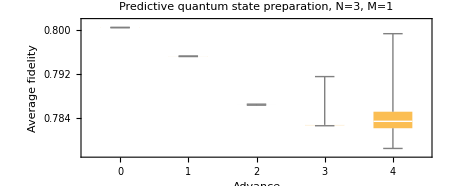
```mathematica
plotCQ=-Graphics-;
```

## 2.2 Panel b: von Neumann entropy

#### Seed

```mathematica
seed=300;
```

#### Parameters for the task

```mathematica
{prep,train,test}={500,2000,500};
delay=2;
{thmax,rmax,φmax}={10.,1.,2.Pi};
```

#### Parameters for QHON generator

```mathematica
n=3;(*was 3*)
ancillas=Range[1];(*was Range[1]*)
{ωbare,g}={0.25,0.1}; 
encoding={{1.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}};(*important! this should be to covariances*)
order=2;
spat=10;(*was 9*)
```

#### Parameters for the task

```mathematica
{prep,train,test}={500,2000,500};
{thmax,rmax,φmax}={10.,1.,2.Pi};
{τmin,τmax}={0,5};
```

#### Reset RNG

```mathematica
(*reset the RNG of all parallel kernels*)
SeedRandom[seed];
listparallelseeds=RandomInteger[{-1000,1000},$KernelCount];
Do[(*seed each subkernel with its own seed*)
ParallelEvaluate[SeedRandom[listparallelseeds[[ker]]],Kernels[][[ker]]],
{ker,$KernelCount}
];
```

#### Compute results

```mathematica
rowreadout=makerowreadout[n,spat,ancillas];
```

```mathematica
(listresultsrow=ParallelTable[
(*create the task*)
listnth=RandomReal[{0.,thmax},prep+train+test];
listr=RandomReal[{0.,rmax},prep+train+test];
listφ=RandomReal[{0.,φmax},prep+train+test];
listinput={listnth,listr,listφ};
listtarget=gettarget[(listnth+0.5)^2,τ];

(*create a QHON instance*)
{update,getinit,preprocess,readout}=makerandomQHON[n,ancillas,ωbare,g,encoding,order,spat];
custompreprocess=makecustompreprocess[preprocess,spat,ancillas,ωbare];
(*get the observables*)
listobservables=getobservables[update,getinit[],custompreprocess,listinput,rowreadout];
getoutput=Last@trainertester[prereadout[listobservables],listtarget,prep,train,test];
listNeumann=listnth Log[1+1/listnth]-Log[1/(1+listnth)];
With[
{(*we use the knowledge that the minimum value of the determinant is 0.25 and add 0.001*)
(*notice that we don't clip it to exactly 0 to avoid probelms with 1/0*)
listnthmaybe=√Clip[getoutput[prereadout[listobservables]],{0.251,∞}]-0.5
},
listNeumannmaybe=listnthmaybe Log[1+1/listnthmaybe]-Log[1/(1+listnthmaybe)]
];
getNMSE[
listNeumannmaybe[[prep+train+1;;prep+train+test]],
listNeumann[[prep+train+1-τ;;prep+train+test-τ]]
],
{realization,realizations},{τ,τmin,τmax}]ᵀ;)//AbsoluteTiming
```

{287.26,Null}

#### Show results

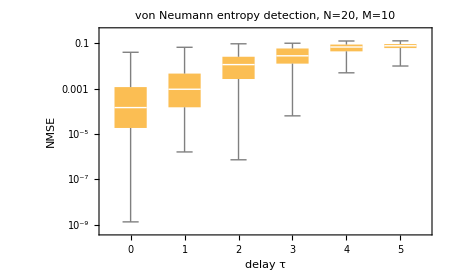

```mathematica
plot2=BoxWhiskerChart[listresultsrow(*,PerformanceGoal->"Speed"*),ImageSize->450,LabelStyle->15,FrameLabel->{"delay τ","NMSE"},PlotRange->All,ChartLabels->Range[τmin,τmax],ScalingFunctions->"Log",PlotLabel->"von Neumann entropy detection, N=20, M=10"]
```

## 2.4 Figure 5

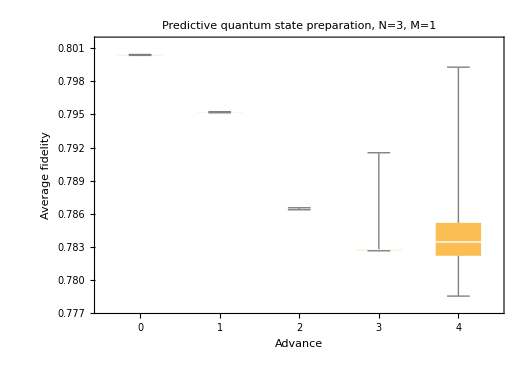
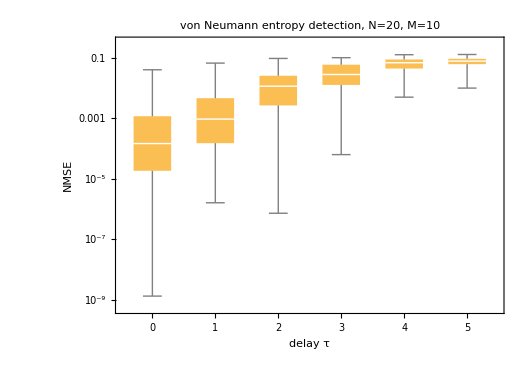
a |  | b
-Graphics- |  | -Graphics-

```mathematica
s=Spacer[30];
aspect=AspectRatio->1/(Sqrt[2]);
plotcombo=Grid[
{{Style["a",20,Bold],"",Style["b",20,Bold]},{Show[plotCQ,ImageSize->525,aspect],s,Show[plot2,ImageSize->525,aspect]}},Alignment->Left
]
```